# Sawtooth wave

```mathematica
Clear[f,fs]
```

### Trigonometric Representation

```mathematica
Period=1;
```

```mathematica
Subscript[y, Min]=0;
```

```mathematica
Subscript[y, Max]=1;
```

```mathematica
f=SawtoothWave[{Subscript[y, Min],Subscript[y, Max]},x/Period];
```

```mathematica
fs=FourierTrigSeries[f,x,5,FourierParameters->{1,(2π)/Period}]
```

1/2-Sin[2 π x]/π-Sin[4 π x]/(2 π)-Sin[6 π x]/(3 π)-Sin[8 π x]/(4 π)-Sin[10 π x]/(5 π)

```mathematica
list1=List@@Normal[fs]
```

{1/2,-Sin[2 π x]/π,-Sin[4 π x]/(2 π),-Sin[6 π x]/(3 π),-Sin[8 π x]/(4 π),-Sin[10 π x]/(5 π)}

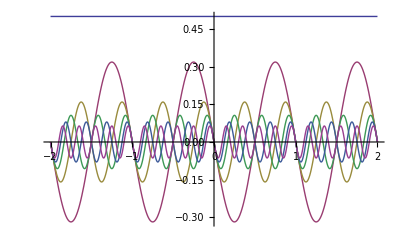

```mathematica
Plot[list1,{x,-2,2}]
```

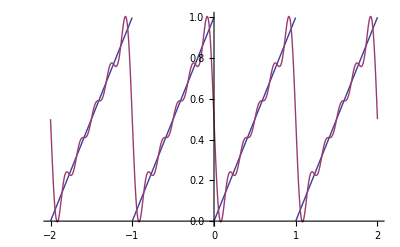

```mathematica
Plot[{f,fs}, {x,-2Period,2Period},PlotRange -> All]
```

### Complex Representation

```mathematica
Clear["Global`*"]
```

The spectral density function

```mathematica
g[k_]:=2/k
```

```mathematica
Table[g[k],{k,2π,10π,2π}]
```

{1/π,1/(2 π),1/(3 π),1/(4 π),1/(5 π)}

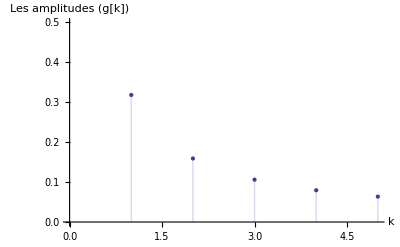

```mathematica
ListPlot[Table[g[k],{k,2π,10π,2π}],Filling->Axis,PlotRange->{0,0.5},AxesLabel->{"k","Les amplitudes (g[k])"}]
```

```mathematica
f[x_]=ⅈ/2-Sum[g[k] ⅇ^(ⅈ  k x),{k,2π,10π,2π}]
```

ⅈ/2-ⅇ^(2 ⅈ π x)/π-ⅇ^(4 ⅈ π x)/(2 π)-ⅇ^(6 ⅈ π x)/(3 π)-ⅇ^(8 ⅈ π x)/(4 π)-ⅇ^(10 ⅈ π x)/(5 π)

```mathematica
list2=Table[g[k] ⅇ^(ⅈ k x),{k,2π,20π,4π}]
```

{ⅇ^(2 ⅈ π x)/π,ⅇ^(6 ⅈ π x)/(3 π),ⅇ^(10 ⅈ π x)/(5 π),ⅇ^(14 ⅈ π x)/(7 π),ⅇ^(18 ⅈ π x)/(9 π)}

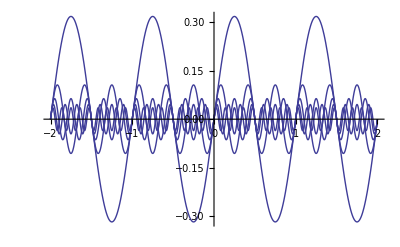

```mathematica
Plot[Im[list2],{x,-2,2}]
```

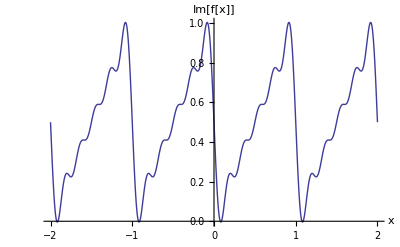

```mathematica
Plot[Im[f[x]],{x,-2,2},AxesLabel->{"x","Im[f[x]]"}]
```

### Play

```mathematica
Play[Im[f[300x]],{x,0,3}]
```

-Graphics-